Geodesic length  L_ε (exact)      = 9.21014

Approximation    2 log(ℓ/ε)       = 9.21034   (Δ = -0.00020003)

RT entropy  S = (c/6) L_ε         = 1.53502   with  ℓ = x_R - x_L

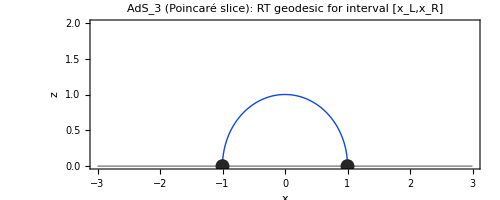

```mathematica
(*----RT in AdS3 Poincaré slice:exact length----*)ClearAll[LgeoExact,LgeoStd,SRT,drawRT];

(*Exact regulated length for interval[xL,xR] with cutoff ε*)
LgeoExact[xL_,xR_,eps_]:=Module[{R=(xR-xL)/2.},If[R<=eps,Indeterminate,2 Log[(R+Sqrt[R^2-eps^2])/eps]                 (* =2 Log[Cot[θmin/2]]*)]];

(*“Textbook” approximation (small ε):L≈2 log(ℓ/ε) with ℓ=xR-xL*)
LgeoStd[xL_,xR_,eps_]:=2 Log[(xR-xL)/eps];

(*RT entropy:S=(c/6) L*)
SRT[c_,xL_,xR_,eps_]:=(c/6) LgeoExact[xL,xR,eps];

(*Picture:boundary and semicircular geodesic with cutoff ε*)
drawRT[xL_:-1,xR_:1,eps_:0.02]:=Module[{c0=(xL+xR)/2.,R=(xR-xL)/2.,θ0,θs,pts},If[R<=eps,Return[Graphics[{},PlotLabel->"Choose ε < ℓ/2"]]];
θ0=ArcSin[eps/R];
θs=Subdivide[θ0+10^-6,Pi-θ0-10^-6,240];
pts=Transpose@{c0+R Cos[θs],R Sin[θs]};
Graphics[{{GrayLevel[.5],Thick,Line[{{-3,0},{3,0}}]},(*boundary*){RGBColor[0.06,0.29,0.86],Thick,Line[pts]},(*geodesic*){GrayLevel[.15],PointSize[.02],Point[{xL,0}],Point[{xR,0}]}  (*endpoints*)},Frame->True,FrameLabel->{"x","z"},PlotRange->{{-3,3},{0,2}},ImageSize->500,PlotLabel->"AdS\!\(_3\) (Poincaré slice): RT geodesic for interval [x_L,x_R]"]];

(*----Example run----*)
xL=-1;xR=1;eps=0.02;cCFT=1.;

Lexact=N@LgeoExact[xL,xR,eps];
Lstd=N@LgeoStd[xL,xR,eps];
Print["Geodesic length  L_ε (exact)      = ",Lexact];
Print["Approximation    2 log(ℓ/ε)       = ",Lstd,"   (Δ = ",Lexact-Lstd,")"];
Print["RT entropy  S = (c/6) L_ε         = ",N@SRT[cCFT,xL,xR,eps],"   with  ℓ = x_R - x_L"];

drawRT[xL,xR,eps]
```

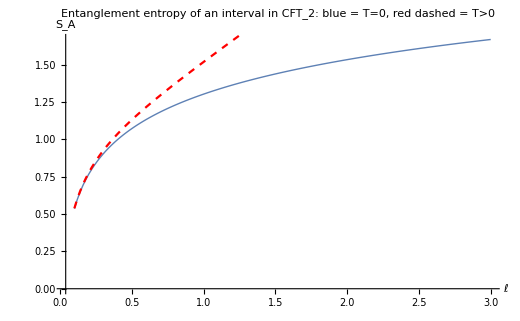

```mathematica
(*----Finite-temperature CFT2 (Euclidean BTZ):S(ℓ) curves----*)ClearAll[SThermal,SZero];

SThermal[c_,ell_,beta_,eps_]:=(c/3) Log[(beta/(Pi eps)) Sinh[Pi ell/beta]];
SZero[c_,ell_,eps_]:=(c/3) Log[ell/eps];

cCFT=1.;eps=0.02;beta=1.5;
ellList=Range[0.1,3.0,0.02];

data0=Table[{ell,SZero[cCFT,ell,eps]},{ell,ellList}];
dataT=Table[{ell,SThermal[cCFT,ell,beta,eps]},{ell,ellList}];

Show[ListLinePlot[data0,PlotStyle->Thick,AxesLabel->{"ℓ","S_A"},ImageSize->520,PlotRange->All,PlotLabel->"Entanglement entropy of an interval in CFT\!\(_2\):  blue = T=0,  red dashed = T>0"],ListLinePlot[dataT,PlotStyle->{Red,Dashed}]]
```